```mathematica
gpdu=Import["G:\\calc-online\\polarized\\juanji\\result\\convolution-rbw-oct-xi1-u-N.wdx"];
Hdgu=Query[1,1]@gpdu;
Heru=Query[1,2]@gpdu;
Hdau=Query[1,3]@gpdu;
Edgu=Query[2,1]@gpdu;
Eeru=Query[2,2]@gpdu;
Edau=Query[2,3]@gpdu;
Hdgfu=Interpolation[Flatten[Hdgu,1]];
Herfu=Interpolation[Flatten[Heru,1]];
Hdafu=Interpolation[Flatten[Hdau,1]];
Edgfu=Interpolation[Flatten[Edgu,1]];
Eerfu=Interpolation[Flatten[Eeru,1]];
Edafu=Interpolation[Flatten[Edau,1]];
```

```mathematica
gpdd=Import["G:\\calc-online\\polarized\\juanji\\result\\convolution-rbw-oct-xi1-d-N.wdx"];
Hdgd=Query[1,1]@gpdd;
Herd=Query[1,2]@gpdd;
Hdad=Query[1,3]@gpdd;
Edgd=Query[2,1]@gpdd;
Eerd=Query[2,2]@gpdd;
Edad=Query[2,3]@gpdd;
Hdgfd=Interpolation[Flatten[Hdgd,1]];
Herfd=Interpolation[Flatten[Herd,1]];
Hdafd=Interpolation[Flatten[Hdad,1]];
Edgfd=Interpolation[Flatten[Edgd,1]];
Eerfd=Interpolation[Flatten[Eerd,1]];
Edafd=Interpolation[Flatten[Edad,1]];
```

```mathematica
Style["H",Black,FontSlant->Italic,FontFamily->Times]
```

H

```mathematica
Style["E",Black,FontSlant->Italic,FontFamily->Times]
```

E

```mathematica
Subsuperscript[OverscriptBox[H,"~"],"u","rbw oct"]//DisplayForm
```

(H̃)_u^(rbw oct)

```mathematica
Subsuperscript[OverscriptBox[H,"~"],"d","rbw oct"]//DisplayForm
```

(H̃)_d^(rbw oct)

```mathematica
Subsuperscript[OverscriptBox[Style["E",Black,FontSlant->Italic,FontFamily->Times],"~"],"u","rbw oct"]//DisplayForm
```

(Ẽ)_u^(rbw oct)

```mathematica
Subsuperscript[OverscriptBox[Style["E",Black,FontSlant->Italic,FontFamily->Times],"~"],"d","rbw oct"]//DisplayForm
```

(Ẽ)_d^(rbw oct)

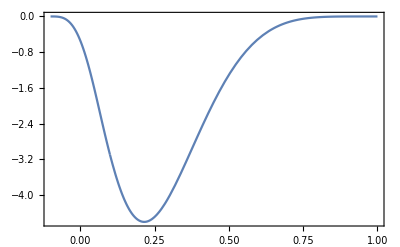
-Graphics-(H̃)_u^(rbw oct)xξ=0.1

```mathematica
picHu=Labeled[Show[Plot[Re[-I*(Herfu[x,-1]+Hdafu[x,-1])],{x,-0.1,0.1},PlotRange->All],Plot[Re[-I*Hdgfu[x,-1]],{x,0.1,1},PlotRange->All],Frame->True,FrameStyle->Directive[Thick,20]],
{"(H̃)_u^(rbw oct)","x","ξ=0.1"},{Left,Bottom,Top},LabelStyle->24]
```

```mathematica
Hdgf1u[0.8,-1]
```

0.-0.0170891 ⅈ

```mathematica
Hdgfu[0.8,-1]
```

9.19434×10^-7-0.0170891 ⅈ

```mathematica
Herf1u[0.05,-1]
```

0.-1.69268 ⅈ

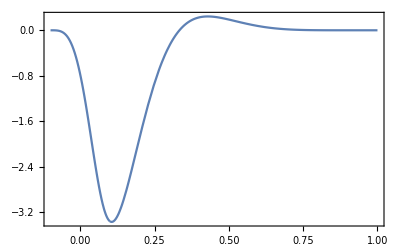
-Graphics-(Ẽ)_u^(rbw oct)xξ=0.1

```mathematica
picEu=Labeled[Show[Plot[Re[-I*(Eerfu[x,-1]+Edafu[x,-1])],{x,-0.1,0.1},PlotRange->All],Plot[Re[-I*Edgfu[x,-1]],{x,0.1,1},PlotRange->All],Frame->True,FrameStyle->Directive[Thick,20]],
{Subscript[OverTilde["E"], "u"]^("rbw oct"),"x","ξ=0.1"},{Left,Bottom,Top},LabelStyle->24]
```

```mathematica
Edgf1u[0.2,-1]
```

0.000430977-1.88208 ⅈ

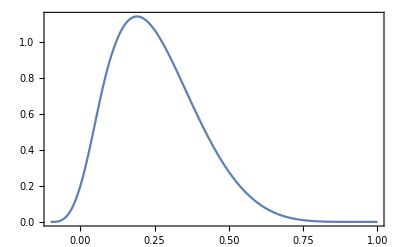
-Graphics-(H̃)_d^(rbw oct)xξ=0.1

```mathematica
picHd=Labeled[Show[Plot[Re[-I*(Herfd[x,-1]+Hdafd[x,-1])],{x,-0.1,0.1},PlotRange->All],Plot[Re[-I*Hdgfd[x,-1]],{x,0.1,1},PlotRange->All],Frame->True,FrameStyle->Directive[Thick,20]],
{Subscript[H̃, "d"]^("rbw oct"),"x","ξ=0.1"},{Left,Bottom,Top},LabelStyle->24]
```

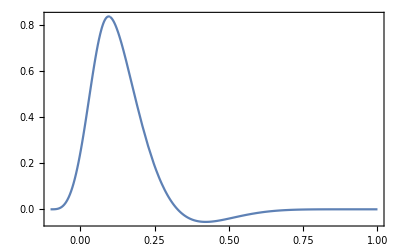
-Graphics-(Ẽ)_d^(rbw oct)xξ=0.1

```mathematica
picEd=Labeled[Show[Plot[Re[-I*(Eerfd[x,-1]+Edafd[x,-1])],{x,-0.1,0.1},PlotRange->All],Plot[Re[-I*Edgfd[x,-1]],{x,0.1,1},PlotRange->All],Frame->True,FrameStyle->Directive[Thick,20]],
{Subscript[OverTilde["E"], "d"]^("rbw oct"),"x","ξ=0.1"},{Left,Bottom,Top},LabelStyle->24]
```

```mathematica
pathHu2d=FileNameJoin[{"G:\\calc-online\\polarized\\juanji\\result","rbw-Hu2d-oct.pdf"}];
Export[pathHu2d,picHu]
```

G:\calc-online\polarized\juanji\result\rbw-Hu2d-oct.pdf

```mathematica
pathHd2d=FileNameJoin[{"G:\\calc-online\\polarized\\juanji\\result","rbw-Hd2d-oct.pdf"}];
Export[pathHd2d,picHd]
```

G:\calc-online\polarized\juanji\result\rbw-Hd2d-oct.pdf

```mathematica
pathEu2d=FileNameJoin[{"G:\\calc-online\\polarized\\juanji\\result","rbw-Eu2d-oct.pdf"}];
Export[pathEu2d,picEu]
```

G:\calc-online\polarized\juanji\result\rbw-Eu2d-oct.pdf

```mathematica
pathEd2d=FileNameJoin[{"G:\\calc-online\\polarized\\juanji\\result","rbw-Ed2d-oct.pdf"}];
Export[pathEd2d,picEd]
```

G:\calc-online\polarized\juanji\result\rbw-Ed2d-oct.pdf